FittedModel[-0.180303+0.00125283 x-1.26141×10^-6 x^2]

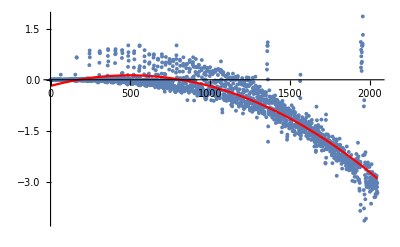

0.863282

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "in-fixed"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a+b*x+c*x^2,{a,b,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
```